Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2021-2022

# Esercizi 5: Attrattore di Lorenz

Notebook del gruppo: pinguini tattici nucleari

Componenti del gruppo: Nicole Mietto e Lorena Escribano Huesca

Se ci sono state collaborazioni e/o aiuti al di fuori del gruppo, dichiararli:
In collaborazione con: 
Aiutato da:

Consegna entro:  10/6/22

```mathematica
SetOptions[EvaluationNotebook[],Background->LightCyan]
```

## Esercizio 5.1: Calcolo dell.b4attrattore di Lorenz

## Testo dell’esercizio

Il sistema di Lorenz (1962) è un sistema dinamico dato da tre equazioni differenziali:

x.b4= σ(y-x)
y.b4= x(r - z) - y
z.b4= x y - β z

Il sistema rappresenta una semplificazione delle equazioni del movimento termico di un fluido. È uno dei primi sistemi dinamici in cui è stata scoperta (e poi dimostrata rigorosamente) l.b4esistenza: i) di traiettorie caotiche, e ii) di un attrattore strano (Tucker 2002).

Sia D lo spazio delle fasi di un sistema dinamico z.b4=F(z). Un sottoinsieme A∈D e detto attrattore del sistema quando:
i) A  e invariante sotto il flusso del sistema Φ_t(A)=A
ii) Esiste un sottoinsieme aperto B∈D, B ≠A, detto il bacino     
     di attrazione di A,tale che, per ogli z∈B si ha lim_(t→∞)Φ_t(z)∈ A. 
Nello studio numerico del sistema di Lorenz si pone σ=10,  β=8/3. Quindi, il sistema è parametrizzato dal valore della costante r. 

Esercizio: 
i) scrivere un integratore numerico del sistema di Lorenz utilizzando la propria funzione RK4 (stessa delle lezioni).
ii) Per ognuno dei valori r=0.3, 0.9, 1. 3,5, 10, 22, 25,28, 40, integrare 10 traiettorie con condizioni iniziali scelte nell.b4insieme (x,y,z) ∈ [[0,5]×[0,5]×[0,5]]. Plottare le traiettorie nello spazio delle fasi (x,y,z). Tempo totale d.b4integrazione: t=50. Incremento: h=0.01.

#### Suggerimenti ed osservazioni:

1. Come si puossono spiegare i risultati? Al variare del valore di r, studiare quanti punti fissi ha il sistema e la loro stabilità lineare. Discutere la presenza di attrattori nei sui grafici. 

2. Presentare i risultati con poche immagini che diano una idea dei comportamenti diversi che si può osservare per le traiettorie ad ogni valore del parametro r.

Nota:
Prima della consegna cancellate gli output dal notebook.
Le immagini verranno ricreate al momento della correzione.

## Soluzione

In questo esercizio verrà studiato il sistema di Lorenz che rappresenta una semplificazione del movimento termico di un fluido nello spazio tridimensionale.

Le equazioni differenziali sono del tipo z’ = X (z) dove z è un elemento dello spazio delle fasi ( Ω ) e X il campo vettoriale.
Definiamo allora il campo vettoriale dell’attrattore di Lorenz che dipende dal vettore nello spazio delle fasi e da un parametro r ( nel nostro caso poichè i parametri σ =10 e β =8/3 sono stati fissati ).

```mathematica
X[{x_,y_,z_},r_]:= {10 (y-x),x (r-z)-y,x y - 8/3 z}
```

Per integrare il sistema di equazioni differenziali ci serviamo del metodo RK4 visto a lezione dove, però, si ha anche la possibilità di inserire tra le variabili r, così non si dovrà ridefinire la funzione ogni volta che si cambia il suo valore.
Questo metodo ci garantisce, come suggerisce il suo nome, una precisione del 4° ordine sull’integrazione numerica.
Vogliamo inoltre rendere l’algoritmo di calcolo più veloce quindi compiliamo le funzioni dell’algoritmo.

Per prima cosa definiamo le funzioni non compilate per poi confrontarne la velocità di esecuzione.

```mathematica
Intstep4[h_,r_][z_]:= Module[{v1,v2,v3,v4},
                  v1=h X[z,r];
                  v2=h X[z+v1/2,r];
                  v3=h X[z+v2/2,r];
                  v4=h X[z+v3,r];
                  z +1/6(v1+2v2+2v3+v4)]
```

```mathematica
Integratore4[z_,tmax_,h_,r_]:=NestList[Intstep4[h,r],z,Floor[tmax/h]]
```

Passiamo ora alla compilazione di Intstep4c.
Come a lezione per RK2, ci serviamo di un Module che contiene la funzione nella forma esplicita. Per ricavare questa formula abbiamo fatto eseguire a Mathematica le espressioni simboliche contenute in Intstep4.

```mathematica
v1=h  X[{x,y,z},r];
v2=h X[{x,y,z}+v1/2,r];
v3=h X[{x,y,z}+v2/2,r];
v4=h X[{x,y,z}+v3,r];
 {x,y,z} +1/6(v1+2v2+2v3+v4);
```

```mathematica
Intstep4c=Compile[{{h,_Real},{r,_Real},{xyz,_Real,1}},
Module[{x,y,z},
x=xyz[[1]];y=xyz[[2]];z=xyz[[3]];
{x+1/6 (10 h (-x+y)+20 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))+20 h (-x+y-5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))+10 h (-x+y-10 h (-x+y-5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))+h (-y-1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z))+(x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (r-z-1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z)))))),y+1/6 (h (-y+x (r-z))+2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z))+2 h (-y-1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z))+(x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (r-z-1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z))))+h (-y-h (-y-1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z))+(x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (r-z-1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z))))+(x+10 h (-x+y-5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))) (r-z-h ((x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (y+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))-8/3 (z+1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z))))))),z+1/6 (h (x y-(8 z)/3)+2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z))+2 h ((x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (y+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))-8/3 (z+1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z))))+h ((x+10 h (-x+y-5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))) (y+h (-y-1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z))+(x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (r-z-1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z)))))-8/3 (z+h ((x+5 h (-x+y-5 h (-x+y)+1/2 h (-y+x (r-z)))) (y+1/2 h (-y-1/2 h (-y+x (r-z))+(x+5 h (-x+y)) (r-1/2 h (x y-(8 z)/3)-z)))-8/3 (z+1/2 h ((x+5 h (-x+y)) (y+1/2 h (-y+x (r-z)))-8/3 (1/2 h (x y-(8 z)/3)+z)))))))}]];
```

Compiliamo ora anche Integratore4c nello stesso modo visto a lezione.

```mathematica
Integratore4c=Compile[{{xyz,_Real,1},{tmax,_Real},{h,_Real},{r,_Real}},
NestList[Intstep4c[h,r,#]&,xyz,Abs[Floor[tmax/h]]]]
```

CompiledFunction[…]

Confrontiamo ora i tempi di calcolo ( il passo h= 0.01, tmax=50  e abbiamo scelto r= 0.3 ).
I tempi di calcolo sono notevolmente migliorati.

```mathematica
Do[Intstep4[0.01,0.3][{0.5,0.5,0.5}],{i,1,100000}]//Timing
Do[Intstep4c[0.01,0.3,{0.5,0.5,0.5}],{i,1,100000}]//Timing
```

{5.73438,Null}

{0.25,Null}

```mathematica
Last[Integratore4[{0.5,0.5,0.5},50,0.01,0.3]]//Timing
Last[Integratore4c[{0.5,0.5,0.5},50,0.01,0.3]]//Timing
```

{0.28125,{7.78833×10^-16,7.26014×10^-16,4.31532×10^-31}}

{0.015625,{7.78833×10^-16,7.26014×10^-16,4.31532×10^-31}}

Troviamo ora la formula generale per i punti fissi del sistema, ossia i punti (x,y,z) che annullano il campo vettoriale.

```mathematica
equilibri=Solve[X[{x,y,z},r]=={0,0,0},{x,y,z}]
```

{{x→0,y→0,z→0},{x→-2 √(2/3) √(-1+r),y→-2 √(2/3) √(-1+r),z→-1+r},{x→2 √(2/3) √(-1+r),y→2 √(2/3) √(-1+r),z→-1+r}}

Osserviamo che :
- se 0≤ r ≤ 1: vi è un unico equilibrio in {0,0,0} poichè se r<1 ho una sola soluzione reale e se r=1 le tre soluzioni coincidono;
- se r>1: vi sono 3 equilibri distinti.

Per studiare la stabilità degli equilibri utilizziamo il primo metodo di Lyapunov:
se zeq è un equilibrio del sistema
- X’(zeq) ha tutti gli autovalori con parte reale negativa allora zeq è asintoticamente stabile;
- X’(zeq) ha almeno un autovalore con parte reale positiva allora zeq è instabile.

Cominciamo dallo studio dell’equilibrio in {0,0,0}.
Poichè r > 0  le radici che si trovano nell’espressione sotto sono numeri reali. Quindi basta assicurarsi, affinchè l’equilibrio sia asintoticamente stabile, che 81+40 r < 121 quindi r < 1 (ossia nei casi r = 0.3 , 0.9 ).
In tutti gli altri casi da analizzare l’equilibrio è instabile ( r = 1. 3, 5, 10, 22, 25,28, 40 )

```mathematica
autoval1= Eigenvalues[D[X[{x,y,z},r],{{x,y,z}}]/.{x->0,y->0,z->0}]
```

{-8/3,1/2 (-11-√(81+40 r)),1/2 (-11+√(81+40 r))}

Studiamo ora il secondo e il terzo equilibrio. 
Semplifichiamo lo studio creando una funzione che dato il valore di r e le regole di sostituzione di un equilibrio restituisce r e la lista delle parti reali di ogni autovalore.

```mathematica
reautoval[r_,eq_]:= {r,Re[Eigenvalues[D[X[{x,y,z},r],{{x,y,z}}]/.eq]]}
```

Mappando la funzione sul secondo equilibrio ( che come il terzo esiste solo per r ≥1 ) notiamo che:
- per r= 25, 28, 40 è instabile;
- per r= 1.3, 5, 10, 22 è asintoticamente stabile.

Mappando la funzione sul terzo equilibrio notiamo che si ottengono gli stessi autovalori del secondo equilibrio.
Quindi le considerazioni di stabilità e instabilità sono le stesse.

```mathematica
autoval2=Map[reautoval[#,equilibri[[2]]/.{r->#}]&,{1.3,5.,10.,22.,25.,28.,40.}]
```

{{1.3,{-11.0766,-1.77729,-0.812745}},{5.,{-11.8092,-0.928724,-0.928724}},{10.,{-12.4757,-0.595497,-0.595497}},{22.,{-13.4938,-0.0864237,-0.0864237}},{25.,{-13.6825,0.00792111,0.00792111}},{28.,{-13.8546,0.0939556,0.0939556}},{40.,{-14.4219,0.377614,0.377614}}}

```mathematica
autoval3=Map[reautoval[#,equilibri[[3]]/.{r->#}]&,{1.3,5.,10.,22.,25.,28.,40.}]
```

{{1.3,{-11.0766,-1.77729,-0.812745}},{5.,{-11.8092,-0.928724,-0.928724}},{10.,{-12.4757,-0.595497,-0.595497}},{22.,{-13.4938,-0.0864237,-0.0864237}},{25.,{-13.6825,0.00792111,0.00792111}},{28.,{-13.8546,0.0939556,0.0939556}},{40.,{-14.4219,0.377614,0.377614}}}

Disegnamo ora 10 orbite per ognuno dei valori di r

Abbiamo deciso di rappresentare l’orbita come dei punti nello spazio tridimensionale mappando la funzione Point di Graphics3D.
In questo modo viene messa in evidenza la velocità di percorrenza dell’orbita (poichè il passo di integrazione è costante ) e quindi eventuali punti di accumulazione ( attrattività dell’orbita in un punto quando vi tende per t→∞ ). 
Per una maggior visualizzazione della stabilità/ instabilità abbiamo colorato gli equilibri.

```mathematica
equilibri2= {x,y,z}/.equilibri
```

{{0,0,0},{-2 √(2/3) √(-1+r),-2 √(2/3) √(-1+r),-1+r},{2 √(2/3) √(-1+r),2 √(2/3) √(-1+r),-1+r}}

Per i primi due valori di r= 0.3, 0.9, come abbaimo già detto vi è un unico equilibrio in 0 che è asintoticamente stabile.
Vediamo che l’equilibrio in 0 è un punto di accumulazione delle orbite selezionate, quindi attrattivo.

```mathematica
or1=Map[Integratore4c[#,50,0.01,0.3] &,{{2.088540264619297,3.3054176153774453,3.363972726116101},{0.11665920984954692,0.9121104528362656,0.36923878707867264},{3.0088146540471037,4.531529097866914,1.6972959844699798},{1.7339196059360473,2.8526026590921347,1.1058004184153525},{2.206702342095854,0.3870617769560596,2.036003686500136},{3.7902790286922556,4.863086170404106,4.360347342596979},{3.1469711367346846,2.7347039677501765,1.4625228109115005},{1.0689425818684057,3.6479692170922142,2.1762183694428874},{2.1014516715075082,1.8939188730431598,4.922287253788207},{3.3883076096254996,0.39805037254187514,3.894781783088284}}];
gr1=Graphics3D[{PointSize->0.001,Map[Point,or1],Magenta,PointSize->Medium,Point[{0,0,0}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=0.3"];
```

```mathematica
or2=Map[Integratore4c[#,50,0.01,0.9] &,{{4.98832314392188,1.2962509070140547,2.0630680404005988},{4.942163213311741,0.8448383517077254,2.7765003554214838},{4.506442905770754,0.6599268575346624,2.0053489053092175},{0.5047544477473114,2.616400108239386,0.778476923558511},{1.3871036330898434,0.38652201164897537,2.360237763105597},{2.621964691643771,3.560325538090435,4.68520496972965},{3.3159718026578613,4.125605319742746,4.603560481870598},{3.854742649905859,3.3658294810584284,1.580978168188981},{0.2589254136738104,2.7318662500776947,3.5016661926640467},{3.1937710567352102,1.414843461825419,3.400282749296956}}];
gr2=Graphics3D[{PointSize->0.001,Map[Point,or2],Magenta,PointSize->Medium,Point[{0,0,0}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=0.9"];
```

```mathematica
GraphicsGrid[{{gr1,gr2}}]
```

-Graphics-

Vediamo ora i grafici per r= 1.3, 5, 10, 22.
Dall’analisi fatta precedentemente ci aspettiamo che l’equilibrio in 0 sia instabile mentre gli altri due siano asintoticamente stabili.

Per i raggi r= 5, 10 non abbiamo trovato delle orbite attrattive al secondo equilibrio per condizioni iniziali in [[0,5]×[0,5]×[0,5]] perciò per verificarne la stabilità abbiamo preso dei punti con componenti negative, mentre nella griglia finale mostreremo solo 10 orbite con le condizioni iniziali indicate.

Infine per ogni grafico abbiamo incluso una condizione iniziale prossima all’origine per mostrarne l’instabilità, l’orbita mostrata parte vicino all’origine ma si allontana da essa (questo non significa che l’origine non possa attrarre nessuna orbita ma basta che in qualsiasi intorno dell’origine ne trovi una instabile per provarne la Lyapunov instabilità ). Nonostante i punti vicino alla condizione iniziale ( prossima all’origine ) sembrano più vicini si osserva che dopo un po’ di tempo l’orbita si distanzia.

```mathematica
or3=Map[Integratore4c[#,50,0.01,1.3] &,{{0.8483793321053383,1.3225870295648514,2.5880130605094385},{0.7755864954533775,4.9203712568586955,3.4804093564839746},{2.1041095129193472,4.862830411225588,4.966531644825821},{2.2051326141771774,3.9331004923816177,2.268783674317124},{4.833109898552459,0.14642614556355227,2.5429817087252538},{2.240568193456581,1.8969686269950579,4.6773749331739864},{2.6760870668162484,0.216033892845382,2.536558332754163},{4.53873183372383,0.9989282207929149,3.1749658224630473},{2.371231546252856,0.41737249473372096,3.5087456560854484},{0.3735399652722222,0.12369788111918378,0.3380780609783782}}];
gr3=Graphics3D[{PointSize->0.001,Map[Point,or3],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->1.3}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->1.3}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=1.3"];
```

```mathematica
or4bis=Map[Integratore4c[#,50,0.01,5] &,{{3.8346047341361515,1.3886814751104932,3.894932707805724},{0.34985432274719486,3.52891955383088,2.627870828403025},{2.306484923334928,-4.4498334034005325,2.208123195712309},{3.413229361479557,-2.7208013737680883,4.54710446683397},{1.8496872478998547,1.7477152162529839,4.371781204654308},{1.4191944350908763,-1.4630353283552697,0.08657027984548904},{0.21665689949958544,1.4268438564589445,0.35568913862154083},{-4.05089865748668636,1.044712142021143,0.},{4.25950223716003,4.534298589468468,1.273092411519393},{0.0440307809534586,0.0784729927092721,0.1718205497807874}}];
gr4bis=Graphics3D[{PointSize->0.001,Map[Point,or4bis],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->5}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->5}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=5"]
```

```mathematica
or4=Map[Integratore4c[#,50,0.01,5] &,{{2.3516414137178234,2.513345900428291,4.500312167604093},{4.6945477716153405,4.456386938476914,4.0379606371749155},{2.8800379550492794,3.8604846284548984,4.84485405224877},{0.47908741552294565,2.303247569669664,4.017278407800166},{2.654394332263638,0.7897567751420818,1.464943560681423},{3.3478732187007516,0.14809496942600298,3.740004793660594},{0.30313894196050484,0.2793969914647949,2.95999486354022},{1.2955978760521516,4.882308028003111,0.9334683187893251},{2.321701556348258,1.3807396515500123,3.5388778942796044},{2.045687270396913,4.942881141360294,3.768372822896511}}];
gr4=Graphics3D[{PointSize->0.001,Map[Point,or4],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->5}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->5}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=5"];
```

```mathematica
or5bis=Map[Integratore4c[#,50,0.01,10] &,{{-3.4061297229474015,1.7946467241950312,1.135335855078928},{1.808380977676192,1.9877355598536557,2.059907234257196},{0.08502673576087574,0.1798748415000215,0.05943443729919213},{3.1190908598221654,-4.827449776944681,1.6031677704863592},{0.9426449264215293,4.778535516894978,4.6060328719839365},{2.0564235042919643,-1.6500387107050791,4.027254466167838},{2.9381850999680683,2.697519467898352,0.5492600168050741},{1.1309557501810428,-1.0156197409894077,0.6367206625846746},{3.5166501776310675,2.7361084630630224,4.997044493831691},{-3.973557886735664,0.24201178103534637,2.5176093730414877}}];
gr5bis=Graphics3D[{PointSize->0.001,Map[Point,or5bis],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->10}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->10}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=10"]
```

```mathematica
or5=Map[Integratore4c[#,50,0.01,10] &,{{2.8470368607013308,4.70229236069758,1.907022315816671},{2.2422490679484,3.6220475996805224,3.9931571910945856},{3.9124562259578575,3.4109963863527035,0.8991822615276304},{2.095671321032273,0.3325399944203591,1.3244453307787136},{0.0347928822470296,0.18215283605552113,0.05797607361120214},{2.66972964417839,4.282269982869774,4.180303813756652},{3.8016693582442365,3.2407370059381044,2.361973334303551},{3.493492866972497,2.925660658399658,4.484772735602709},{2.8501585630380255,2.8837686199226145,0.5265958361668721},{3.047099541470917,4.23356968322528,4.382840199575087}}];
gr5=Graphics3D[{PointSize->0.001,Map[Point,or5],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->10}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->10}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=10"];
```

```mathematica
or6=Map[Integratore4c[#,50,0.01,22] &,{{1.7545757106255166,3.4558779077913897,4.418566286802383},{0.4251442613632559,3.73073771184265,4.796062548775065},{2.085411413480318,3.252236669938336,2.8981580802307985},{1.2581014453033532,2.782503292325373,3.1096819601254513},{1.6293162661848415,3.3302094724420535,3.034710689963811},{3.891036750707988,0.19531177507046582,3.8042178172046732},{2.3652587999569192,1.1620314768310962,0.5936711230702372},{0.2191076074551708,0.023436873364292232,0.07062923293891448},{2.206905257072945,0.829764559071978,2.741554507359063},{3.7785240901211896,0.7910305396791708,2.3158731151607537}}];
gr6=Graphics3D[{PointSize->0.001,Map[Point,or6],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->22}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->22}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=22"];
```

```mathematica
GraphicsGrid[{{gr3,gr4},{gr5,gr6}},ImageSize->Large]
```

Infine per r=25, 28, 40 vi sono solo equilibri instabili.
L’attrattore di Lorenz non è più un punto ma un’intera regione dello spazio (dai grafici ).

```mathematica
or7=Map[Integratore4c[#,50,0.01,25] &,{{1.2125457065931302,1.9449603512422078,2.7342940999249477},{2.1932461387572406,4.665027171613179,3.094567306791795},{1.127069678270277,0.9246094389794717,1.6133891179132505},{2.077955454836191,1.082197103433126,1.7248543764619564},{1.0198106437203656,3.356543349942731,3.174548674612952},{4.513265642028889,4.592258120307724,2.9905267662343036},{2.2095898644520195,0.6796380961961219,3.4635626659121},{0.090908710300236,0.03557159576447937,0.0603355199550933},{3.877076820577267,0.8692415322802578,0.7384180288873914},{3.2670856844201364,4.791743915840458,1.1543473798825747}}];
gr7=Graphics3D[{PointSize->0.001,Map[Point,or7],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->25}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->25}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=25"];
```

```mathematica
or8=Map[Integratore4c[#,50,0.01,28] &,{{2.510510456745507,3.989027406024725,0.7364850869367014},{1.355171667223459,1.245119200484007,4.689216735324539},{4.0133219317567725,0.8993908655078817,0.302242033783914},{1.542248887980584,4.969595532359982,0.022904162467584754},{2.4316945056446,1.8565044542645648,3.092969470206718},{0.6224470085868363,1.6195987493462107,3.9092164732169525},{0.0945876501737823,0.1357528565358006,0.0231067738660121},{2.9662407581027352,1.4381233065701347,0.8775346060267903},{3.584311905318039,2.013284276788866,0.6208824715614476},{4.2464141122855565,4.102156013081684,2.247500406002291}}];
gr8=Graphics3D[{PointSize->0.001,Map[Point,or8],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->28}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->28}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=28"];
```

```mathematica
or9=Map[Integratore4c[#,50,0.01,40] &,{{4.104327118401784,3.6248133498458674,1.7133430021432252},{2.461903097233815,2.0111440432699847,3.200106439805495},{3.9268775468883295,2.9321215479137486,4.202168945360903},{1.3264595373355714,0.05193042243281454,4.704919775598119},{2.831726115783333,2.7410115352505002,4.933320153088822},{0.9771616402155718,4.879085277140433,1.9305717909506246},{3.3963425480537257,1.7168189753037355,2.179060076598116},{0.30823657307785446,4.261566349455524,0.06765707519500008},{1.6336193252437017,4.237493396747665,3.178122272841197},{0.687019307630945,2.930704373530279,0.6062834454287946}}];
gr9=Graphics3D[{PointSize->0.001,Map[Point,or9],Magenta,PointSize->Medium,Point[{0,0,0}],PointSize->Medium,Green,Point[equilibri2[[2]]/.{r->40}],PointSize->Medium,Red,Point[equilibri2[[3]]/.{r->40}]},Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"r=40"];
```

```mathematica
GraphicsGrid[{{gr7,gr8,gr9}},ImageSize->Large]
```

## Esercizio 5.2: Calcolo dell.b4esponente di Lyapunov per l.b4attrattore di Lorenz

## Testo dell’esercizio

i) Includere nell’integratore RK4 anche le equazioni alle variazioni per il sistema di Lorenz

ii) Calcolare l.b4esponente di Lyapunov di una traiettoria con condizioni iniziali (x,y,z)=(1.5,0.5,0.4) nel caso r=23, r=25, r=28, r=30. Ripetere il calcolo per la stessa condizione iniziale (x,y,z), variando, però, il vettore tangente iniziale ζ. Ripetere per altre condizioni iniziali (x,y,z). Cosa osserviamo?

#### Suggerimenti ed osservazioni:

Studiare quale dev.b4essere il tempo d.b4integrazione per stabilizzare il valore di χ(t) nel caso di una traiettoria caotica.

Per poter osservare meglio la stabilizzazione, plottare log χ(t) vs log t

## Soluzione

Per descrivere il distanziamento di sue soluzioni ( z_t e y_t ) di un sistema di equazioni differenziali con punti iniziali vicini si può approssimare la distanza in questo modo: z_t - y_t =  Φ_t(z_0) - Φ_t(y_o)  ≈   Φ_t’(z_0) ( z_0-y_0)  ( con Φ_t flusso al tempo t ).

Come visto a lezione si dimostra che  (ζ̇)_t = d/dt∂/(∂z)Φ_t(z_0)ζ_0= X'(z_t) ζ_t   con ζ_t= z_t - y_t e ζ_0= z_0-y_0   ( chiamata equazione alle variazioni ), perciò ζ_t è soluzione del sistema  (ż)_t=X(z_t),  (ζ̇)_t= X'(z_t) ζ_t  con dati iniziali z_0 e ζ_0. 

Vogliamo includere in RK4, definita nell’esercizio precedente anche le equazioni alle variazioni per il sistema di Lorenz.

Innanzitutto  definiamo  X'(z), la chiameremo J,  che viene utilizzata nell’equazione alle variazioni ( si tratta della matrice Jacobiana di X calcolata in z in R^3 ).
Definiamo poi il nuovo campo vettoriale Y del sistema di equazioni che intendiamo risolvere.

```mathematica
J[{a_,b_,c_},r_]:= D[X[{x,y,z},r],{{x,y,z}}]/.{x->a,y->b,z->c}
```

```mathematica
Y[{a_,b_,c_,d_,e_,f_},r_]:= Flatten[{X[{a,b,c},r],J[{a,b,c},r].{d,e,f}}]
```

Ridefiniamo RK4 per Y esattamente come nell’esecizio precedente ma con un diverso campo vettoriale

```mathematica
(* l'espressione sotto è stata ricavata da qui *)
v1=h Y[{x,y,z,a,b,c},r];
v2=h Y[{x,y,z,a,b,c}+v1/2,r];
v3=h Y[{x,y,z,a,b,c}+v2/2,r];
v4=h Y[{x,y,z,a,b,c}+v3,r];
                  {x,y,z,a,b,c} +1/6(v1+2v2+2v3+v4)//Simplify;
```

```mathematica
Intstep4c2=Compile[{{h,_Real},{r,_Real},{xyzabc,_Real,1}},
Module[{x,y,z,a,b,c},
x=xyzabc[[1]];
y=xyzabc[[2]];
z=xyzabc[[3]];
a=xyzabc[[4]];
b=xyzabc[[5]];
c=xyzabc[[6]];
{x+5/216 h (9 h^3 (-1+5 h) x^3 (2-10 h+5 h^2 (10+r-z)) (r-z)+y (432-2376 h-2475 h^6 y^2-6 h^3 (3333+660 r-820 z)+72 h^2 (111+10 r-10 z)+40 h^5 (135 y^2+88 z)-20 h^4 (45 y^2+296 z))-3 h^2 x^2 y (24-268 h-10 h^3 (220+67 r-67 z)+10 h^2 (107+9 r-9 z)+75 h^4 (10+22 r+r^2-22 z-2 r z+z^2))+x (-432-24 h^2 (300+63 r-71 z)+675 h^6 y^2 (7+4 r-4 z)+216 h (10+r-z)+40 h^4 (105 y^2+2 (71+3 r-3 z) z)-5 h^5 (3 y^2 (811+60 r-60 z)+64 (10+r-z) z)+2 h^3 (9000+90 r^2-270 y^2-3697 z+90 z^2-9 r (-321+20 z)))),y+1/6 h (-6 y+x (r-z)+2 (x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+h (-r x+y+x z)+1/2 h (2 y-2 (x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)-h (-r x+y+x z))+2 (x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+1/2 h (2 y+h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))-2 (x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z))))+(x+5/6 h (3 h^2 (-1+5 h) x^2 y+y (12-66 h+h^2 (333+30 r-30 z)+40 h^3 z)-x (12+h^2 (300+63 r-71 z)-6 h (10+r-z)+5 h^3 (3 y^2+8 z)))) (r-z+8/3 h (z-2/9 h (3 h x y+6 z-8 h z)+1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))-h (x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))))),z+1/6 h (x y-(8 z)/3-8/9 (3 h x y+6 z-8 h z)+2 (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z))+2 (-8/3 (z-2/9 h (3 h x y+6 z-8 h z)+1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))))-8/3 (z-8/3 h (z-2/9 h (3 h x y+6 z-8 h z)+1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+h (x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))))+(x+5/6 h (3 h^2 (-1+5 h) x^2 y+y (12-66 h+h^2 (333+30 r-30 z)+40 h^3 z)-x (12+h^2 (300+63 r-71 z)-6 h (10+r-z)+5 h^3 (3 y^2+8 z)))) (y+h (-y-1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))))),a-5/216 h (2 c h (-20 h (-18+123 h-148 h^2+88 h^3) y+x (108-852 h+1350 h^5 y^2+h^2 (3697+180 r-180 z)+10 h^4 (160+16 r-45 y^2-32 z)-40 h^3 (71+3 r-6 z))+9 h^2 (-1+5 h) x^3 (1-5 h+5 h^2 (5+r-z))-15 h^3 x^2 y (9-67 h+15 h^2 (11+r-z)))+a (432+24 h^2 (300+63 r+6 x y-71 z)-216 h (10+r-z)-20 h^4 (210 y^2+284 z-27 x^2 z-12 z^2+3 r (9 x^2-9 x y+4 z)+3 x y (-107+9 z))-2 h^3 (9000+90 r^2+804 x y-270 y^2-3697 z+27 x^2 z+90 z^2-9 r (-321+3 x^2+20 z))+5 h^5 (27 r^2 x^2+2433 y^2+640 z-180 y^2 z+27 x^2 (-20+z) z-64 z^2+r (-804 x y+180 y^2-54 x^2 (-10+z)+64 z)+12 x y (-220+67 z))-225 h^6 (r^2 x (3 x-2 y)+r (12 y^2+4 x y (-11+z)-6 x^2 (-5+z))+3 y^2 (7-4 z)+3 x^2 (-10+z) z-2 x y (10-22 z+z^2)))+b (-432+2376 h+6 h^3 (3333+660 r-134 x^2+180 x y-820 z)-72 h^2 (111+10 r-x^2-10 z)+10 h^4 (-840 x y+270 y^2+3 x^2 (107+9 r-9 z)+592 z)-10 h^5 (3 x^2 (220+67 r-67 z)-3 x y (811+60 r-60 z)+4 (405 y^2+88 z))+225 h^6 (33 y^2-6 x y (7+4 r-4 z)+x^2 (10+22 r+r^2-22 z-2 r z+z^2)))),b+1/6 h (-6 b-c x+1/3 ((-1+5 h) x-5 h y) (c (6-8 h)+3 h (b x+a y))+a (r-z)-1/3 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+h (b+c x+a (-r+z))-h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z)))+2 (a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+(a-10 a h+10 b h-25 h^2 (b (2-11 h)-c h x+a (-2+h (10+r-z)))+5 h^2 (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z)))) (r-z+8/3 h (z-2/9 h (3 h x y+6 z-8 h z)+1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))-h (x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))))+2 (-x+5/2 h ((-2+11 h) y+x (2+h (-10-r+z)))) (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z)))))-h (-b-1/2 h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z)))+(a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+(-x+5/2 h ((-2+11 h) y+x (2+h (-10-r+z)))) (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z))))))+(-x-5/6 h (3 h^2 (-1+5 h) x^2 y+y (12-66 h+h^2 (333+30 r-30 z)+40 h^3 z)-x (12+h^2 (300+63 r-71 z)-6 h (10+r-z)+5 h^3 (3 y^2+8 z)))) (c+h ((a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z)))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (b+1/2 h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z))))-8/3 (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z)))))))),c+1/6 h (-(8 c)/3+b x+a y+8/9 (c (-6+8 h)-3 h (b x+a y))-(a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+2 (x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z)))+(a-10 a h+10 b h-25 h^2 (b (2-11 h)-c h x+a (-2+h (10+r-z)))+5 h^2 (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z)))) (y+h (-y-1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))))+2 ((a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z)))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (b+1/2 h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z))))-8/3 (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z))))))-8/3 (c+h ((a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (y+1/2 h (-y+(x-5 h x+5 h y) (r-(h x y)/2-z+(4 h z)/3)+1/2 h (-r x+y+x z)))+(x+5/2 h ((2-11 h) y+x (-2+h (10+r-z)))) (b+1/2 h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z))))-8/3 (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z)))))))+(x+5/6 h (3 h^2 (-1+5 h) x^2 y+y (12-66 h+h^2 (333+30 r-30 z)+40 h^3 z)-x (12+h^2 (300+63 r-71 z)-6 h (10+r-z)+5 h^3 (3 y^2+8 z)))) (b+h (-b-1/2 h (-b+((-1+5 h) x-5 h y) (c+1/2 h (-(8 c)/3+b x+a y))-1/6 (a-5 a h+5 b h) (-6 r+3 h x y+6 z-8 h z)+1/2 h (b+c x+a (-r+z)))+(a-5 a h-5/2 h (b (-2+11 h)+c h x)+5/2 a h^2 (10+r-z)) (r-z+2/9 h (3 h x y+6 z-8 h z)-1/2 h (x-5 h x+5 h y) (y-1/2 h (-r x+y+x z)))+(-x+5/2 h ((-2+11 h) y+x (2+h (-10-r+z)))) (c+1/2 h (4/9 (c (-6+8 h)-3 h (b x+a y))-1/2 (a-5 a h+5 b h) (-2 y+h (-r x+y+x z))+(x-5 h x+5 h y) (b-1/2 h (b+c x+a (-r+z))))))))}]]
```

CompiledFunction[…]

```mathematica
Integratore4c2=Compile[{{xyzabc,_Real,1},{tmax,_Real},{h,_Real},{r,_Real}},
NestList[Intstep4c2[h,r,#]&,xyzabc,Abs[Floor[tmax/h]]]]
```

CompiledFunction[…]

Con le modifiche apportate alle funzioni usate nell’esercizio 1 si riesce ad integrare il campo Y (z, ξ) = ( X(z) , X’ (z) ξ ) con ξ vettore tangente.

L.b4esponente caratteristico di Lyapunov (Lyapunov characteristic exponent (LCE) è  il limite (quando esiste)
                                          lim_(t→∞)  χ(t),   dove   χ(t) = 1/tln(ξ(t)/ξ(0)) 
Per studiare l’LCE bisgona introdurre la dipendenza dal tempo.

Definiamo:
-Y che calcola il generico campo vettoriale Y (z, ξ) = ( X(z) , X’ (z) ξ ) al variare del parametro r
-la funzione lorenz che integra numericamente il campo vettoriale Y, costruita in modo analogo a quanto visto a lezione per le equazioni di Lagrange

```mathematica
Clear[t]
```

```mathematica
Y[r_]:= Y[{x[t],y[t],z[t],i[t],j[t],k[t]},r];
lorenz[z0_,zet0_,T_,r_]:=NDSolve[{D[x[t],t]==Y[r][[1]],D[y[t],t]==Y[r][[2]],D[z[t],t]==Y[r][[3]],D[i[t],t]==Y[r][[4]],D[j[t],t]==Y[r][[5]],D[k[t],t]==Y[r][[6]],x[0]==z0[[1]],y[0]==z0[[2]],z[0]==z0[[3]],i[0]==zet0[[1]],j[0]==zet0[[2]],k[0]==zet0[[3]]},{x,y,z,i,j,k},{t,0,T},MaxSteps->Infinity];
```

Definiamo la funzione chi, la quale mette insieme con un Module le seguenti operazioni:
-Calcolo dell’orbita orb
-Assegnazione di i, j, k del campo vettoriale Y
-Calcolo della norma di ξ
-Grafico di χ (t) = 1/t In (xi(t)) , che al limite da il valore dell’ esponente di Lyapunov.

```mathematica
chi[datoin_,vettg_,r_,col_]:=Module[{orb,it,jt,kt,xi},
                                                                            orb=lorenz[datoin, vettg,750.,r];
                                                                            {it,jt,kt}={i/.orb[[1]],j/.orb[[1]],k/.orb[[1]]};
                                                                             xi[t_]=Sqrt[it[t]^2+jt[t]^2+kt[t]^2];
                                                                             Plot[(1/t)*Log[xi[t]],{t,0,750},PlotRange->{-.4,1},PlotStyle->col]]
```

Se  χ(t) si stabiliza ad un valore positivo, questo valore da una stima del LCE. 
Se, invece, χ(t) decresce con t, questo indica che l’orbita non è caotica.

Fissata la condizione iniziale (x, y, z) = (1.5, 0.5, 0.4) studiamo l’ LCE e il tempo necessario per la stabilizzazione al variare di diversi vettori tangenti iniziali vettg1 e vettg2.

```mathematica
datoin={1.5,.5,.4};
vettg1= {1.2,.3,.5};
vettg2= {.5,.1,-.3};
```

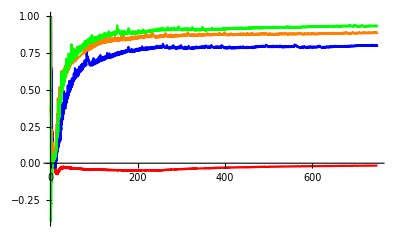

```mathematica
Show[chi[datoin,vettg1,23,Red],chi[datoin,vettg1,25,Blue],
         chi[datoin,vettg1,28,Orange],chi[datoin,vettg1,30,Green]]
```

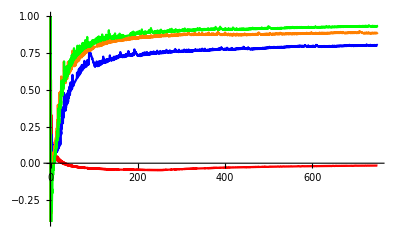

```mathematica
Show[chi[datoin,vettg2,23,Red],chi[datoin,vettg2,25,Blue],
         chi[datoin,vettg2,28,Orange],chi[datoin,vettg2,30,Green]]
```

Fissato il vettore tangente iniziale (x, y, z) = (0.5, 0.6, 0.4) studiamo l’ LCE e il tempo necessario per la stabilizzazione al variare di diverse condizioni iniziali

```mathematica
vettg= {.5,.6,.4};
datoin1= {2,.6,.4};
datoin2={.2,10,4};
```

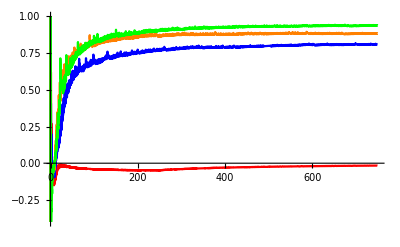

```mathematica
Show[chi[datoin1,vettg,23,Red],chi[datoin1,vettg,25,Blue],
         chi[datoin1,vettg,28,Orange],chi[datoin1,vettg,30,Green],PlotLegends->Automatic]
```

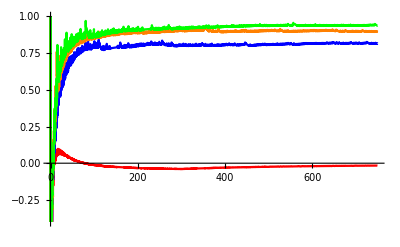

```mathematica
Show[chi[datoin2,vettg,23,Red],chi[datoin2,vettg,25,Blue],
          chi[datoin2,vettg,28,Orange],chi[datoin2,vettg,30,Green]]
```

I valori dell’esponente caratteristico di Lyapunov sono:
r = 23 : -0.01
r = 25 : 0.8
r = 28 : 0.9
r = 30 : 0.95
Il tempo di stabilizzazione varia tra 250 e 300.

Dai grafici osserviamo che al variare delle condizioni e vettori tangenti iniziali i valori dell’esponente di Lyapunov e del tempo restano sostanzialmente invariati. 
I grafici che corrispondono a r = 25, 28, 30 hanno un andamento simile e i corrispondenti LCE differiscono di poco. 
Per r = 23 si ha invece un andamento completamente diverso con un LCE negativo.
In conclusione, per r = 23 gli equilibri sono stabili. Invece per r = 25, 28, 30 si perde la stabilità.